## Background

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv"];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

```mathematica
Dimensions[rawXs]
```

{52,210352}

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

## Algorithm

In Group, Missing for less than X time, reappear in group -> count as group member

In Group, Missing for more than X time, reappear in group -> does not count as group member

Group is considered different if there have been more than X edits within X time

```mathematica
dbScanHerds50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx"];
```

```mathematica
dbScanHerds10=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds10.mx"];dbScanHerds30=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds30.mx"];
```

```mathematica
dbScanHerds50
```

{{{5,8,17,21,22,33,35,38,40,44,48},{}},{{2,3,4,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,29,31,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,51},{}},210348,{{2},{5,40,51},{7,8},{12,44,50},{16,39},{21},{31,46},{}}}
 |  |  |  |

```mathematica
dbScanHerds50[[1000]]
```

{{2,4,5,6,8,10,11,17,22,23,26,28,29,31,32,35,40,41,44,45,46,49},{3,7,9,20,21,36,38,48},{12,14,16,18,24,25,33,34,37,39,42,47,51},{}}

```mathematica
dbScanHerds50[[1100]]
```

{{2,4,5,6,8,10,11,17,22,23,26,27,28,29,31,32,35,40,41,44,45,46,49},{3,7,9,20,21,36,38,48},{12,14,18,33,47,51},{16,24,25,34,37,39,42},{}}

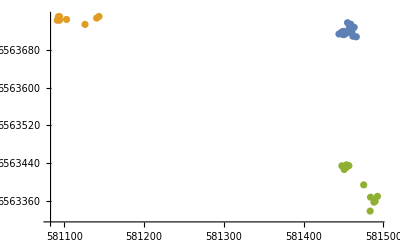

```mathematica
ListPlot[rawCoordinates[[#,1000]]&/@Most[dbScanHerds50[[1000]]]]
```

```mathematica
dbScanHerds50LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds50;
```

```mathematica
dbScanHerds10LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds10
```

{{{5,8,17,21,22,33,35,38,40,44,48}},{{2,3,4,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,29,31,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,51}},210348,{{2},{5},{7},{8},{12},{16},{21},{31},{39},{40},{44},{46},{50},{51}}}
 |  |  |  |

```mathematica
dbScanHerds20LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds20
```

{{{5,8,17,21,22,33,35,38,40,44,48}},{{2,3,4,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,29,31,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,51}},210348,{{2},{5},{7},{8},{12},{16},{21},{31},{39},{40},{44},{46},{50},{51}}}
 |  |  |  |

```mathematica
dbScanHerds50LonelySheep[[1230]]
```

{{3,5,7,8,9,10,11,20,21,22,23,26,28,29,31,32,35,36,38,41,44,45,46,48,49},{12,14,16,18,24,25,33,34,37,39,42,47,51},{2},{4},{17},{40}}

```mathematica
Manipulate[Show[metadataGraphic,ListPlot[rawCoordinates[[#,n]]&/@dbScanHerds50LonelySheep[[n]]],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}},ImageSize->650],{n,1000,2000,1}]
```

```mathematica
dbScanHerds50[[1231]]
```

{{2,4,17,40},{3,5,7,8,9,10,11,20,21,22,23,26,28,29,31,32,35,36,38,41,44,45,46,48,49},{12,14,16,18,24,25,33,34,37,39,42,47,51},{}}

```mathematica
dbScanHerds50[[1232]]
```

{{3,5,8,9,10,20,22,23,28,29,31,32,35,36,38,41,44,45,46,48,49},{12,14,16,18,24,25,33,34,37,39,42,47,51},{2,4,11,17,26,40}}

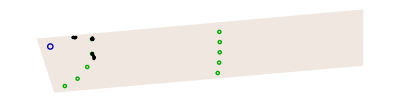

```mathematica
Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,1000]],1,2],PlotRange->RegionBounds[paddockRegion]]]
```

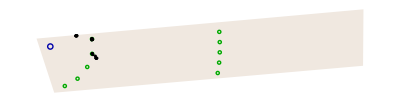

```mathematica
Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,1100]],1,2],PlotRange->RegionBounds[paddockRegion]]]
```

## Group Stability

```mathematica
groupStability50=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds50LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupStability10=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds10LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupStability20=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds20LonelySheep,{2}]],First->Last,Join];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability50.mx",groupStability50];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability10.mx",groupStability10];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability20.mx",groupStability20];
```

```mathematica
groupStability50
```

<|{5,8,17,21,22,33,35,38,40,44,48}→{1},{2,3,4,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,29,31,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,51}→{2},11034,{12,44,50}→{210351},{31,46}→{210351}|>
 |  |  |  |

```mathematica
Keys[SortBy[groupStability50,Length[Last[#]]&]][[;;200]]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{1,5},{1,9},{1,24},{1,46},{2,3},{2,8},{2,9},{2,10},{2,19},{2,22},{2,23},{2,26},{2,29},{2,37},{2,41},{2,46},{3,4},{3,20},{3,33},{4,11},{4,13},{4,14},{4,16},{4,23},{4,27},{4,35},{4,43},{4,50},{5,8},{5,14},{5,17},{5,28},{5,30},{5,36},{5,37},{5,46},{6,30},{6,33},{6,44},{6,46},{7,8},{7,10},{7,28},{7,48},{8,22},{8,28},{8,32},{8,33},{8,48},{9,15},{9,37},{9,38},{9,41},{10,12},{10,17},{10,48},{11,13},{11,21},{11,23},{11,39},{11,45},{12,42},{13,25},{13,45},{14,50},{15,43},{15,49},{16,21},{16,22},{16,28},{16,35},{16,39},{16,43},{17,20},{17,30},{17,38},{17,41},{17,46},{18,35},{18,51},{21,36},{21,43},{22,38},{24,25},{26,35},{26,36},{26,45},{27,39},{27,45},{28,29},{28,48},{29,39},{29,46},{31,41},{31,46},{31,49},{32,48},{33,46},{34,37},{35,42},{35,50},{36,44},{37,41},{37,43},{39,41},{40,43},{42,48},{44,45},{44,47},{46,51},{47,49},{1,2,11},{1,3,15},{1,3,26},{1,3,29},{1,3,40},{1,3,41},{1,4,11},{1,4,46},{1,5,46},{1,9,16},{1,9,30},{1,10,35},{1,24,29},{1,32,37},{1,32,44},{1,39,43},{2,3,4},{2,3,45},{2,3,50},{2,4,45},{2,11,21},{2,11,41},{2,14,26},{2,15,33},{2,16,35},{2,16,42},{2,24,29},{2,26,28},{2,28,35},{2,29,39},{2,31,41},{2,32,35},{2,36,50},{2,41,47},{2,46,50},{3,4,43},{3,5,39},{3,6,19}}

```mathematica
biggerHerds=Length/@KeySelect[ReverseSortBy[groupStability50,Length],Length[#]>5&];
```

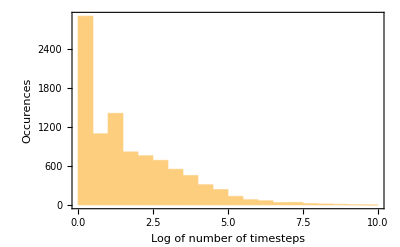

```mathematica
Histogram[Log[Values[biggerHerds]],Frame->True,FrameLabel->{{"Occurences",""},{"Log of number of timesteps","stability distribution groups larger than 5"}}]
```

```mathematica
Length/@ReverseSortBy[groupStability50,Length][[;;10]]
```

<|{2}→36868,{46}→28529,{22}→23039,{16}→22185,{23}→21234,{11}→20256,{31}→18373,{27}→18062,{13}→16911,{1}→16767|>

```mathematica
Length/@KeySelect[SortBy[groupStability50,Length],Length[#]==1&][[;;51]]
```

<|{19}→2667,{50}→2963,{4}→3852,{51}→4138,{21}→5707,{41}→6126,{24}→6885,{48}→6924,{8}→7196,{32}→8791,{28}→8871,{17}→8923,{14}→8966,{25}→9428,{12}→9656,{18}→9965,{15}→10357,{29}→10636,{44}→10808,{47}→10856,{37}→10979,{35}→11531,{9}→11552,{34}→11568,{10}→11849,{49}→12171,{5}→12785,{26}→13631,{40}→13653,{42}→14077,{30}→14145,{33}→14488,{38}→14739,{36}→15145,{45}→15161,{6}→15385,{39}→15422,{7}→15503,{3}→15594,{20}→15945,{43}→16729,{1}→16767,{13}→16911,{27}→18062,{31}→18373,{11}→20256,{23}→21234,{16}→22185,{22}→23039,{46}→28529,{2}→36868|>

## Group Network

downsample + section

80% of sheep join the same group in the next timestep ->

80% sourced from the previous stimestep

do single sheep first

At this step, there is very little data: 105103, 157490

```mathematica
FindRulesFromTo[first_,second_,firstindex_,threshold_]:=
Module[{r},
r=Reap[
Table[If[(Length[c1]-Length[Complement[c1,c2]])/Length[c1]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]];If[(Length[c2]-Length[Complement[c2,c1]])/Length[c2]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]],{c1,first},{c2,second}]];
If[Flatten[DeleteCases[r,{Null},2]]==={},{},DeleteDuplicates[r[[2,1]]]
]]
```

```mathematica
FindFissionFusionGraph[tmin_,tmax_,threshold_,lonelySheep_]:=Graph[Catenate[Table[FindRulesFromTo[lonelySheep[[a]],lonelySheep[[a+1]],a,threshold],{a,tmin,tmax}]]];
```

```mathematica
g10=FindFissionFusionGraph[700,800,0.8,dbScanHerds10LonelySheep];
```

```mathematica
g20 =FindFissionFusionGraph[700,800,0.8,dbScanHerds20LonelySheep];
```

```mathematica
g50=FindFissionFusionGraph[700,800,0.8,dbScanHerds50LonelySheep];
```

```mathematica
dbScanHerds10===dbScanHerds20
```

True

```mathematica
fullg50=FindFissionFusionGraph[1,210350,0.8,dbScanHerds50LonelySheep];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/FullStabilityGraph.mx",fullg]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/FullStabilityGraph.mx

Trying to contract edges:

```mathematica
contractEdges[g_]:=EdgeContract[g,Select[EdgeList[g],VertexDegree[g,#[[1]]]===2||VertexDegree[g,#[[2]]]===2&]]
```

```mathematica
Graph[g,VertexLabels->(#->If[Divisible[Last[#],10],Last[#]]&/@VertexList[g])]
```

Set::write: Tag Inherited in Inherited[State] is Protected.

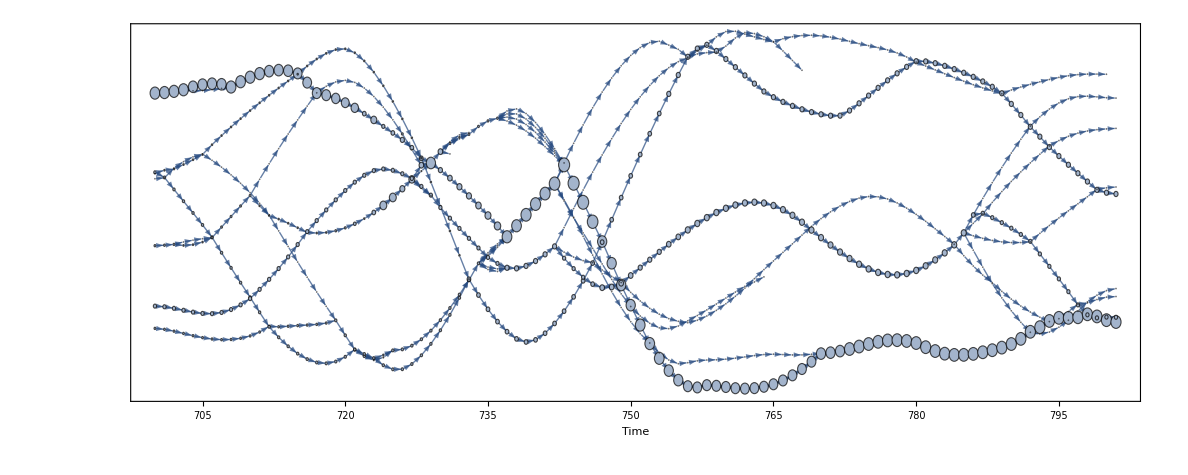

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[g,VertexSize->(#->Length[First[#]]*3&/@VertexList[g]),VertexCoordinates->(#->{Last[#],Automatic}&/@VertexList[g]),Frame->True,FrameTicks->{True,False},FrameLabel->{Style["Time",Large],None}]
```

```mathematica
connected=ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]];
```

```mathematica
connected=ConnectedComponents[UndirectedGraph[Subgraph[fullg,Select[VertexList[fullg],VertexDegree[fullg,#]===2&]]]];
```

```mathematica
connected[[1]][[-1,2]]
```

800

```mathematica
fullgStability=Union[Catenate[#[[All,1]]]]->#[[-1,2]]-#[[1,2]]&/@connected;
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability50.mx",fullgStability]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability50.mx

```mathematica
fullgStability[[1]]
```

{23}→7373

```mathematica
Mean[DeleteMissing[rawCoordinates[[{1,3,4},200,2]]]]
```

6.56357×10^6

```mathematica
trainingData=RandomSample[DeleteMissing[Catenate[rawCoordinates],1,2],10000];
tsne=DimensionReduction[trainingData,1,Method-> "TSNE"];
```

```mathematica
tsne[rawCoordinates[[2,1;;10]]]
```

{{7.69737},{79.2529},{79.2535},{79.2542},{79.2547},{79.2553},{79.2561},{79.2574},{79.2585},{79.2592}}

```mathematica
coloredGraph[g_,enlargingFactor_]:=HighlightGraph[Graph[g,VertexSize->(#->Length[First[#]]*enlargingFactor&/@VertexList[g]),VertexCoordinates->(#->{Last[#]/10,Mean[DeleteMissing[rawCoordinates[[#[[1]],Last[#],2]]]]/100}&/@VertexList[g]),Frame->True,FrameTicks->True,EdgeShapeFunction->"Line",FrameLabel->{Style["Time in min since the start of data collection",Large],None}],ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]]
```

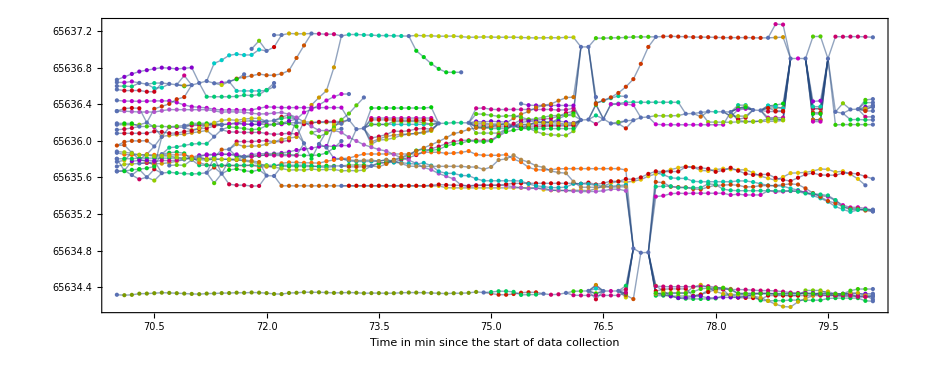

```mathematica
coloredGraph[g10,10000000]
```

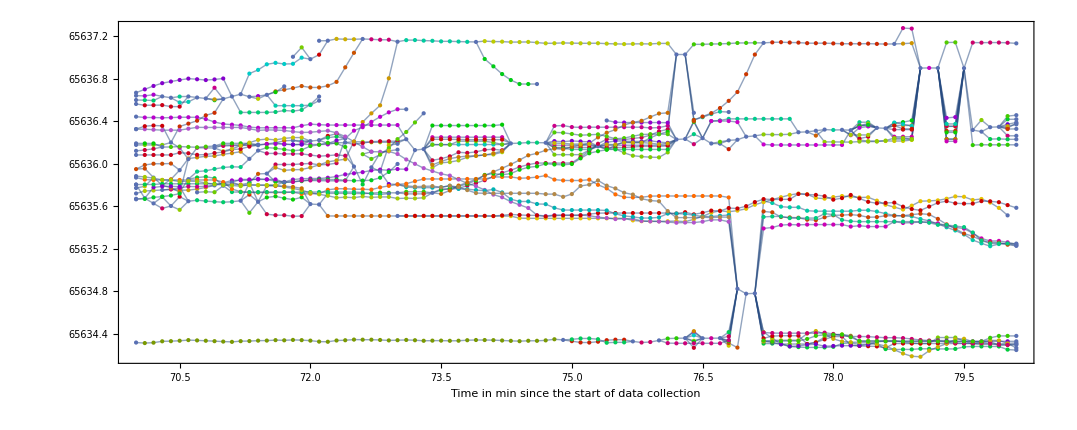

```mathematica
coloredGraph[g20,1000000]
```

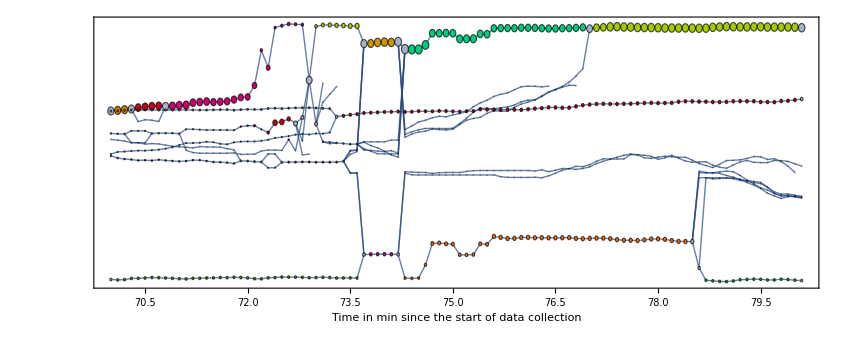

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
coloredGraph[g50,20]
```

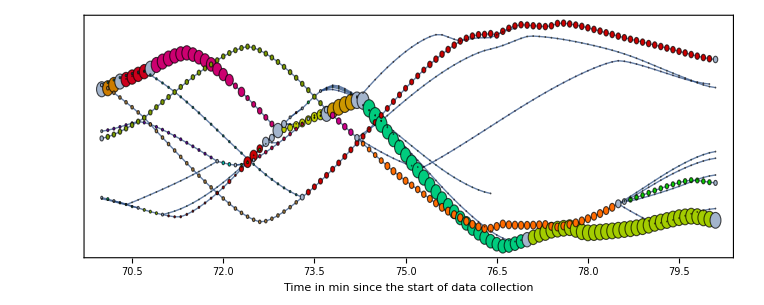

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
g2=Module[{paths,pathsg,endpoints},
paths=ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]];
pathsg=NeighborhoodGraph[g,#]&/@paths;
endpoints=Function[pg,DirectedEdge@@Select[VertexList[pg],VertexDegree[pg,#]===1&]]/@pathsg;
EdgeAdd[VertexDelete[g,Catenate[paths]],endpoints]
]
```

-Graphics-

```mathematica
Graph[g2,VertexSize->(#->Length[First[#]]/10&/@VertexList[g2]),(*VertexLabels->(#->Last[#]&/@VertexList[g2]),*)VertexCoordinates->(#->{Last[#],Automatic}&/@VertexList[g2])]
```

-Graphics-

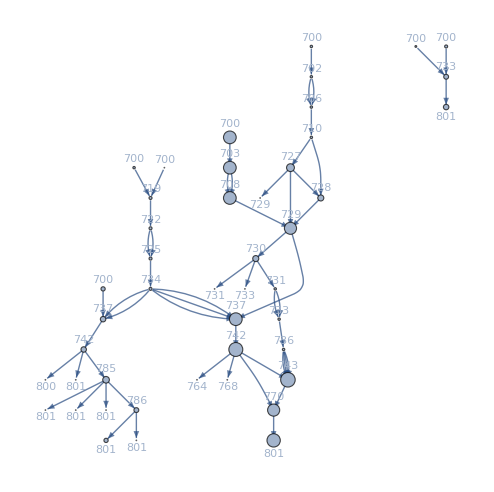

```mathematica
Graph[g2,VertexSize->(#->Length[First[#]]*0.02&/@VertexList[g2]),VertexLabels->(#->Last[#]&/@VertexList[g2]),GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
VertexDelete[g,EdgeList[g][[1]]]===g
```

True

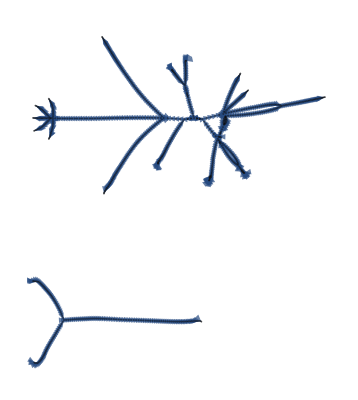

```mathematica
EdgeContract[g,Select[EdgeList[g],VertexDegree[g,#[[2]]]===2&]]
```

```mathematica
Fold[VertexContract,g,Select[VertexList[g],VertexDegree[g,#]===2&]]
```

-Graphics-

```mathematica
VertexList[g][[1]]
```

{{1,2,4,5,6,10,11,13,17,22,23,26,27,28,29,35,40,41,44,45,46},700}

```mathematica
(Length[First[#]]&/@VertexList[g])
```

{21,21,3,3,4,4,5,5,4,4,7,7,1,1,21,3,4,5,4,7,1,21,3,4,5,3,1,7,1,20,1,3,4,5,3,7,1,1,20,3,4,5,3,7,1,1,1,20,3,4,5,4,7,1,1,20,3,4,5,4,7,1,1,21,3,4,5,4,7,1,21,3,4,5,4,7,1,21,3,4,5,4,7,1,21,3,4,5,3,1,7,1,20,3,4,5,3,7,1,1,20,3,4,5,3,7,1,1,20,3,4,5,3,7,1,1,19,3,4,5,3,7,1,1,19,3,4,5,3,7,1,1,19,3,4,5,3,7,1,1,19,3,4,5,3,7,1,1,18,3,5,5,4,7,1,17,3,5,5,4,7,1,16,3,5,5,6,7,1,8,3,5,5,3,7,1,13,3,2,3,5,8,7,1,7,3,15,2,5,3,7,1,8,3,15,5,5,7,1,9,3,11,5,5,7,4,8,3,13,5,5,1,7,8,3,2,10,1,5,5,7,20,3,5,5,7,1,9,10,3,5,5,7,10,3,4,1,1,5,5,7}

## Influence of threshold

```mathematica
gstrict=FindFissionFusionGraph[700,800,0.99];
```

```mathematica
HighlightGraph[Graph[gstrict,VertexSize->(#->Length[First[#]]*15&/@VertexList[gstrict]),VertexCoordinates->(#->{Last[#]/10,Automatic}&/@VertexList[gstrict]),Frame->True,FrameTicks->{True,False},FrameLabel->{Style["Time in min since the start of data collection",Large],None},EdgeShapeFunction->"Line",AspectRatio->1/4],ConnectedComponents[UndirectedGraph[Subgraph[gstrict,Select[VertexList[gstrict],VertexDegree[gstrict,#]===2&]]]]]
```

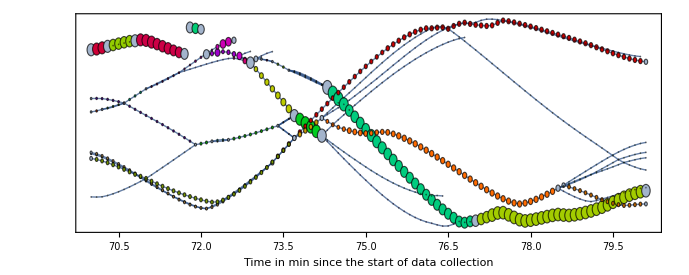

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
gloose=FindFissionFusionGraph[700,800,0.2];
```

```mathematica
HighlightGraph[Graph[gloose,VertexSize->(#->Length[First[#]]*20&/@VertexList[gloose]),VertexCoordinates->(#->{Last[#],Automatic}&/@VertexList[gstrict]),Frame->True,FrameTicks->{True,False},FrameLabel->{Style["Time",Large],None},AspectRatio->1/3.5],ConnectedComponents[UndirectedGraph[Subgraph[gloose,Select[VertexList[gloose],VertexDegree[gloose,#]===2&]]]]]
```

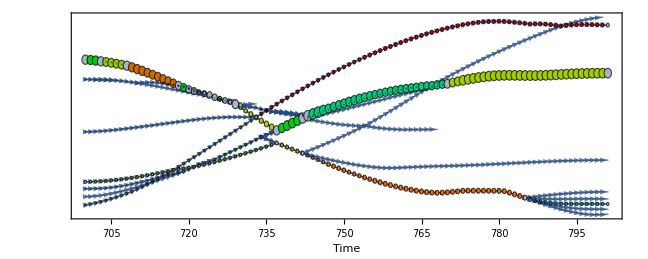

Set::write: Tag Inherited in Inherited[State] is Protected.